### 第一题

## 我的答案：

```mathematica
list=Table[n,{n,1,100}];
Do[If[Mod[list[[i]],3]==0&&Mod[list[[i]],5]==0,list[[i]]=Graphics[{Red,Rectangle[]},ImageSize->{10,10}]];
If[Mod[list[[i]],3]==0,list[[i]]=Graphics[{Black,Rectangle[]},ImageSize->{10,10}]];
If[Mod[list[[i]],5]==0,list[[i]]=Graphics[{Blue,Rectangle[]},ImageSize->{10,10}]],
{i,1,100}];
list
```

{1,2,-Graphics-,4,-Graphics-,-Graphics-,7,8,-Graphics-,-Graphics-,11,-Graphics-,13,14,-Graphics-,16,17,-Graphics-,19,-Graphics-,-Graphics-,22,23,-Graphics-,-Graphics-,26,-Graphics-,28,29,-Graphics-,31,32,-Graphics-,34,-Graphics-,-Graphics-,37,38,-Graphics-,-Graphics-,41,-Graphics-,43,44,-Graphics-,46,47,-Graphics-,49,-Graphics-,-Graphics-,52,53,-Graphics-,-Graphics-,56,-Graphics-,58,59,-Graphics-,61,62,-Graphics-,64,-Graphics-,-Graphics-,67,68,-Graphics-,-Graphics-,71,-Graphics-,73,74,-Graphics-,76,77,-Graphics-,79,-Graphics-,-Graphics-,82,83,-Graphics-,-Graphics-,86,-Graphics-,88,89,-Graphics-,91,92,-Graphics-,94,-Graphics-,-Graphics-,97,98,-Graphics-,-Graphics-}

## 视频答案：

```mathematica
Range@100/.{x_/;Divisible[x,3]&&Divisible[x,5]->Red,x_/;Divisible[x,5]->White,x_/;Divisible[x,3]->Black}
```

{1,2,GrayLevel[0],4,GrayLevel[1],GrayLevel[0],7,8,GrayLevel[0],GrayLevel[1],11,GrayLevel[0],13,14,RGBColor[1, 0, 0],16,17,GrayLevel[0],19,GrayLevel[1],GrayLevel[0],22,23,GrayLevel[0],GrayLevel[1],26,GrayLevel[0],28,29,RGBColor[1, 0, 0],31,32,GrayLevel[0],34,GrayLevel[1],GrayLevel[0],37,38,GrayLevel[0],GrayLevel[1],41,GrayLevel[0],43,44,RGBColor[1, 0, 0],46,47,GrayLevel[0],49,GrayLevel[1],GrayLevel[0],52,53,GrayLevel[0],GrayLevel[1],56,GrayLevel[0],58,59,RGBColor[1, 0, 0],61,62,GrayLevel[0],64,GrayLevel[1],GrayLevel[0],67,68,GrayLevel[0],GrayLevel[1],71,GrayLevel[0],73,74,RGBColor[1, 0, 0],76,77,GrayLevel[0],79,GrayLevel[1],GrayLevel[0],82,83,GrayLevel[0],GrayLevel[1],86,GrayLevel[0],88,89,RGBColor[1, 0, 0],91,92,GrayLevel[0],94,GrayLevel[1],GrayLevel[0],97,98,GrayLevel[0],GrayLevel[1]}

### 第二题

```mathematica
array=Array[0*#&,{50,50}];
Do[Do[If[Mod[i,j]==0&&i≥j,array[[i,j]]=1],{i,1,50}],{j,1,50}]
ArrayPlot[array]
```

-Graphics-

## 视频答案:

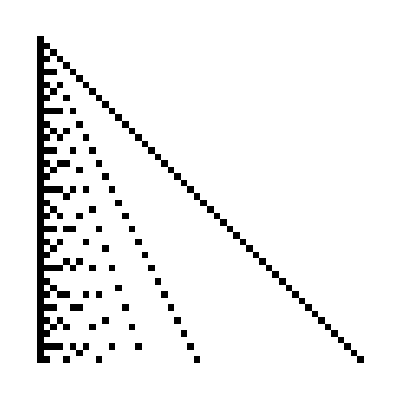

```mathematica
ArrayPlot[Array[List,{50,50}]/.{{x_,y_}/;Divisible[x,y]->Black,{x_,y_}->White}]
```

### 第三题

```mathematica
t=Now;
array=Table[i+j,{i,1000},{j,0,999}];
Do[Do[If[Mod[array[[i,j]],7]==0||MemberQ[IntegerDigits[array[[i,j]]],7],array[[i,j]]=1],{i,1,1000}],{j,1,1000}]
ArrayPlot[array,ColorRules->{1->Red,_->White}]
Now-t
```

-Graphics-

3.81537 s

## 视频答案：

```mathematica
t=Now;
dat=Divisible[#,7]||MemberQ[IntegerDigits[#],7]&/@Range@1000;
ArrayPlot@Boole@Outer[And,dat,dat]
Now-t
```

-Graphics-

0.396275 s

### 第四题

```mathematica
base=Range[100,999];
data={};
Do[Do[If[base[[i]]*base[[j]]==IntegerReverse[base[[i]]*base[[j]]],AppendTo[data,{base[[i]]*base[[j]],base[[i]],base[[j]]}]],{i,1,Length[base]}],{j,1,Length[base]}];
less=Last@Sort[Table[data[[i,1]],{i,Length[data]}]];
Select[data,#[[1]]==less&]
```

{{906609,993,913},{906609,913,993}}

## 视频答案：

```mathematica
Catch@Do[If[Module[{l=IntegerDigits[t]},l==Reverse@l],Throw[t]],{t,SortBy[Flatten[Table[i j,{i,999,100,-1},{j,999,i,-1}],1],-#&]}]
906609
```

### 第五题：

```mathematica
base=RandomInteger[100,{20,20}];
data2={};
heng=Last@Sort[Map[Sum[#[[i]],{i,1,4}]&,Flatten[Partition[base,{1,4},1],2]]];
shu=Last@Sort[Map[Sum[#[[i]],{i,1,4}]&,Flatten[Partition[Transpose@base,{1,4},1],2]]];
Do[Do[If[i≤(20-3)&&j≤(20-3),AppendTo[data2,base[[i,j]]+base[[i+1,j+1]]+base[[i+2,j+2]]+base[[i+3,j+3]]]],{i,1,20}],{j,1,20}];
xie=Last@Sort[data2];
Max@Sort[{heng,shu,xie}]
```

363

## 视频答案:

```mathematica
tab=Partition[RandomInteger[20,{20,20}],{4,4},{1,1}];
Map[{Total/@#,Total/@Transpose@#,Total@Diagonal@#,Total@Diagonal@Reverse@#}&,tab,{2}]//Flatten//Max
```

74

### 第六题(看不懂啊）

```mathematica
t=Now;
Clear[f];
n=1000;
f[1]={{1}};
f[n_]:=f[n]=Module[{sel=Reap[Do[If[Not@FreeQ[j,n-1],Sow@j],{i,Floor[n/2],n-1},{j,f[i]}]][[2,1]],ls},
ls=Length/@sel;
ArrayPad[Pick[sel,ls,Max@ls],{{0,0},{0,1}},n]];
Total[Length[f[#][[1]]]&/@Range@n]-n
Now-t
```

499500

2.7226 s